This notebook contains a number of different things, among which:
1) Utilities to load data from JSON files obtained from numerical training. Mind that these JSON files were obtained using a previous version of the python code, and may not be compatible with the current version.
2) Testing with generators for various gates. Some or most of this code may not be working anymore due to changes in GateLearning.m (it should be easily fixable though).

# Functions definitions

```mathematica
Needs["QM`"];
Needs["utilities`"];
Needs["GeneralUtilities`"];

PrependTo[$Path,NotebookDirectory[]];
<<QPauliAlgebra`
<<GateLearning`

SetOptions[$FrontEnd,IgnoreSpellCheck->True]

p[n_,m_,numQubits_:1]:=Normal@SparseArray[{n,m}->1,{#,#}&[2^numQubits]];
KP[expr___]:=KroneckerProduct[expr];
SetOptions[MatrixPlot,{ImageSize->300,Mesh->All,PlotRangePadding->None}];

highlightPauliOps[expr_]:=expr/.{s:(𝒳|𝒴|𝒵)[n_]:>Style[s,Red,Bold]};
```

# Results

## CNOT

```mathematica
Normal[QPauliSymbolicProduct[x[2]+z[1]]]//TraditionalForm
```

(1 | 1 | 0 | 0
1 | 1 | 0 | 0
0 | 0 | -1 | 1
0 | 0 | 1 | -1)

```mathematica
π/16 QPauliSymbolicProduct[1-z[1]-z[2]-z[3]-x[4]+z[1]z[2]+z[1]z[3]+z[1]x[4]+z[2]z[3]+z[2]x[4]+z[3]x[4]-z[1]z[2]z[3]-z[1]z[2]x[4]-z[1]z[3]x[4]-z[2]z[3]x[4]+z[1]z[2]z[3]x[4]]//Normal//MatrixExp[ⅈ #]&
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

```mathematica
decomposeLogWithPaulis@CNot[]
```

π/4-1/4 π 𝒳[2]-1/4 π 𝒵[1]+1/4 π 𝒳[2] 𝒵[1]

```mathematica
cnotGenerator=QPauliSymbolicProduct@Distribute@Simplify[4/π decomposeLogWithPaulis@CNot[]]
```

1-𝒳[2]-𝒵[1]+𝒵[1]𝒳[2]

```mathematica
QPauliSymbolicProduct[1+x[2]+z[1]+z[1]x[2]]
```

1+𝒳[2]+𝒵[1]+𝒵[1]𝒳[2]

```mathematica
MatrixForm@MatrixExp[ⅈ π/4 QPauliSymbolicProduct[1+x[2]+z[1]+z[1]x[2]]]
```

(0 | -1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
#·#·#&@cnotGenerator
```

16 1-16 𝒳[2]-16 𝒵[1]+16 𝒵[1]𝒳[2]

```mathematica
With[{
ℋ=QPauliSymbolicProduct[1-x[2]-z[1]+z[1]x[2]]
},
Manipulate[
MatrixExp[ⅈ θ ℋ]//MatrixForm//First//Chop//Abs//barChart3D[#,RotationAction->"Clip"]&,
{{θ,0.01},0.001,Pi/2,0.01,Appearance->"Labeled"}
]
]
```

```mathematica
Chop@pauliBasis[m]
```

1/2 (2.18039 ℐ[1]+1.06338 𝒳[1]-0.971513 𝒴[1]+0.760751 𝒵[1])

```mathematica
Chop@pauliBasis[
#.#†&@RandomComplex[{-#,#}&[1+I],{#,#}&@4]
]//Distribute
```

1.69126 ℐ[1] ℐ[2]+0.495251 ℐ[2] 𝒳[1]-0.36798 ℐ[1] 𝒳[2]-0.380388 𝒳[1] 𝒳[2]-0.21429 ℐ[2] 𝒴[1]+0.0489006 𝒳[2] 𝒴[1]+0.519946 ℐ[1] 𝒴[2]-0.276173 𝒳[1] 𝒴[2]+0.00382801 𝒴[1] 𝒴[2]+0.313478 ℐ[2] 𝒵[1]+0.280165 𝒳[2] 𝒵[1]-0.422254 𝒴[2] 𝒵[1]+0.457596 ℐ[1] 𝒵[2]+0.472581 𝒳[1] 𝒵[2]+0.264103 𝒴[1] 𝒵[2]+0.247472 𝒵[1] 𝒵[2]

```mathematica
QPauliSymbolicProduct@decomposeLogWithPaulis@PauliProduct[2,2,3]
```

(π 1)/2-1/2 π 𝒴[1]𝒴[2]𝒵[3]

```mathematica
MatrixExp[ⅈ θ QPauliSymbolicProduct[x[1]+y[2]]]
```

MatrixExp[ⅈ θ (𝒳[1]+𝒴[2])]

```mathematica
Normal[
π/4 QPauliSymbolicProduct[1-z[1]-z[2]+z[1]z[2]]
]//MatrixExp[ⅈ #]&
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)

```mathematica
Normal@QPauliSymbolicProduct[x[1]x[2]+y[1]y[2]+z[1]z[2]]
```

(1 | 0 | 0 | 0
0 | -1 | 2 | 0
0 | 2 | -1 | 0
0 | 0 | 0 | 1)

```mathematica
MatrixExp[ⅈ θ Normal@QPauliSymbolicProduct[x[1]x[2]+y[1]y[2]+z[1]z[2]]]
```

(ⅇ^(ⅈ θ) | 0 | 0 | 0
0 | ⅇ^(ⅈ θ)/2+1/2 ⅇ^(-3 ⅈ θ) | ⅇ^(ⅈ θ)/2-1/2 ⅇ^(-3 ⅈ θ) | 0
0 | ⅇ^(ⅈ θ)/2-1/2 ⅇ^(-3 ⅈ θ) | ⅇ^(ⅈ θ)/2+1/2 ⅇ^(-3 ⅈ θ) | 0
0 | 0 | 0 | ⅇ^(ⅈ θ))

```mathematica
Manipulate[
MatrixExp[ⅈ θ Normal@QPauliSymbolicProduct[x[1]x[2]+y[1]y[2]+z[1]z[2]]]//Abs//barChart3D,
{{θ,0},0,2Pi,0.01,Appearance->"Labeled"}
]
```

## Toffoli gate

### Canonical generator for Toffoli

The “Hamiltonian generators” of the Toffoli are -𝒵_1,-𝒵_2,𝒳_3.
Notice that the π/8 arises from there being 8 terms in the corresponding expression.

```mathematica
toffoliGenerator=QPauliSymbolicProduct@decomposeLogWithPaulis@Toffoli[]//Simplify
```

1/8 π (1-𝒳[3]-𝒵[1]-𝒵[2]+𝒵[1]𝒳[3]+𝒵[1]𝒵[2]+𝒵[2]𝒳[3]-𝒵[1]𝒵[2]𝒳[3])

```mathematica
QPauliSymbolicProduct@decomposeLogWithPaulis@Toffoli[]/.s_[e_]:>e/.pauliOps[s__]:>s//FullSimplify
```

1/8 π (1-𝒵[1]-𝒳[3] (-1+𝒵[1]) (-1+𝒵[2])+(-1+𝒵[1]) 𝒵[2])

```mathematica
8/π Normal@toffoliGenerator//TraditionalForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 4 | -4
0 | 0 | 0 | 0 | 0 | 0 | -4 | 4)

```mathematica
Normal[
QPauliSymbolicProduct[1-z[1]]·QPauliSymbolicProduct[1-z[2]]·QPauliSymbolicProduct[1-x[3]]
]//TraditionalForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 4 | -4
0 | 0 | 0 | 0 | 0 | 0 | -4 | 4)

The above Hamiltonian evolution satisfies ℋ^2=π ℋ

```mathematica
toffoliGenerator·toffoliGenerator//Simplify
```

1/8 π^2 (1-𝒳[3]-𝒵[1]-𝒵[2]+𝒵[1]𝒳[3]+𝒵[1]𝒵[2]+𝒵[2]𝒳[3]-𝒵[1]𝒵[2]𝒳[3])

```mathematica
QPauliSymbolicProduct@Chop@decomposeLogWithPaulis[
N@HadamardMatrix[8]
]
```

1.5708 1-0.55536 𝒵[2]-0.55536 𝒳[1]𝒵[3]-0.55536 𝒳[2]𝒳[3]+0.55536 𝒴[1]𝒴[3]-0.55536 𝒵[1]𝒳[2]+0.55536 𝒳[1]𝒴[2]𝒴[3]+0.55536 𝒴[1]𝒴[2]𝒵[3]-0.55536 𝒵[1]𝒵[2]𝒳[3]

```mathematica
MatrixForm@toffoliGenerator
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | π/2 | -π/2
0 | 0 | 0 | 0 | 0 | 0 | -π/2 | π/2)

See how the result of the MatrixExp operation oscillates back and forth between identity and Toffoli gate:

```mathematica
Manipulate[
MatrixExp[ⅈ θ 8/π toffoliGenerator]//MatrixForm//First//Chop//Abs//barChart3D[#,RotationAction->"Clip"]&,
{{θ,0.01},0.001,Pi/4,0.01,Appearance->"Labeled"}
]
```

```mathematica
TraditionalForm@Normal@Toffoli[]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

## Fredkin

### Canonical generator of Fredkin gate

```mathematica
Fredkin[]//Normal//TraditionalForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
fredkinGenerator=8/π QPauliSymbolicProduct@decomposeLogWithPaulis@Fredkin[]//Simplify
```

(8 QPauliSymbolicProduct[decomposeLogWithPaulis[SparseArray[<8>, {8, 8}]]])/π

```mathematica
MatrixForm@Normal@fredkinGenerator
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 4 | -4 | 0
0 | 0 | 0 | 0 | 0 | -4 | 4 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Manipulate[
MatrixExp[ⅈ θ 8/π Normal@fredkinGenerator]//Chop//Abs//barChart3D[#,RotationAction->"Clip"]&,
{{θ,0.01},0.001,Pi/4,0.01,Appearance->"Labeled"}
]
```

### Doubly-controlled-Fredkin on 3+1 qubits space, canonical generator

Let us consider a 3+1 qubits gate, with the gate acting as a Fredkin on the system when the ancilla is 0, and as anti-Fredkin on the system if the ancilla is 1:

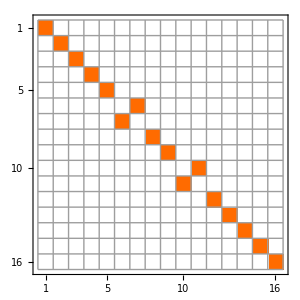

```mathematica
alternativeFredkin=Plus[KP[p[2,2],IdentityMatrix@4],
KP[p[1,1],Swap[]]];

niceFredkinTarget=Plus[KP[p[1,1],Fredkin[]],
KP[p[2,2],alternativeFredkin]];

niceFredkinTarget//MatrixPlot
```

The direct decomposition with MatrixLog gives a decomposition involving fourth order interactions, that can be understood as the swap (implemented by the term (1-Heisenberg_(3,4)) ) happening on the central space on which the projector (-1+𝒵_1 𝒵_2)/2 projects. More precisely, the obtained generator is π P ℋ_SWAP, with 2P=1-𝒵_1 𝒵_2 and 4 ℋ_SWAP=1-(𝒳_1 𝒳_2+𝒴_1 𝒴_2+𝒵_1 𝒵_2).

```mathematica
niceFredkinNaiveGenerator=Simplify@Expand@QPauliSymbolicProduct@decomposeLogWithPaulis@niceFredkinTarget

decomposeLogWithPaulis@niceFredkinTarget//FullSimplify
```

QPauliSymbolicProduct[decomposeLogWithPaulis[{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}}]]

decomposeLogWithPaulis[{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}}]

```mathematica
MatrixExp[ⅈ π Normal[
Expand@QPauliSymbolicProduct[1/4(1-x[1]x[2]+y[1]y[2]+z[1]z[2])]
]]//TraditionalForm
```

(0 | 0 | 0 | 1
0 | 1 | 0 | 0
0 | 0 | 1 | 0
1 | 0 | 0 | 0)

```mathematica
With[{ℋ=Normal[
QPauliSymbolicProduct@decomposeLogWithPaulis@niceFredkinTarget
]},
Manipulate[
MatrixExp[ⅈ θ ℋ]//Abs//barChart3D,
{{θ,0},0,1,0.01,Appearance->"Labeled"}
]
]
```

```mathematica
QPauliSymbolicProduct@decomposeLogWithPaulis@niceFredkinTarget
```

(π 1)/8-1/8 π 𝒳[3]𝒳[4]-1/8 π 𝒴[3]𝒴[4]-1/8 π 𝒵[1]𝒵[2]-1/8 π 𝒵[3]𝒵[4]+1/8 π 𝒵[1]𝒵[2]𝒳[3]𝒳[4]+1/8 π 𝒵[1]𝒵[2]𝒴[3]𝒴[4]+1/8 π 𝒵[1]𝒵[2]𝒵[3]𝒵[4]

### Doubly-controlled-Fredkin on 3+1 qubits space, pairwise interactions taken from training

On the other hand, we know that this unitary can be also generated by an Hamiltonian with only pairwise interactions (thanks to the maximization procedure).

```mathematica
loadInteractionTermsFromJSON[
FileNameJoin@{
"C:\\Users\\lk\\Documents\\docs\\coding\\python\\quantum-gate-learning",
"data","nets","fredkin_best.json"
},
{2,3,4,1}
]
```

<|{2,z}→-0.000333662,{3,z}→6.29587×10^-6,{4,z}→-0.0000157899,{1,z}→0.0000957945,{{2,3},xx}→0.348637,{{2,3},xy}→0.958271,{{2,3},xz}→-3.31681,{{2,3},yx}→0.0496028,{{2,3},yy}→0.24456,{{2,3},yz}→-0.690827,{{2,3},zx}→0.323379,{{2,3},zy}→0.655609,{{2,3},zz}→-1.81265,{{2,4},xx}→0.347624,{{2,4},xy}→0.956952,{{2,4},xz}→-3.31586,{{2,4},yx}→0.0493772,{{2,4},yy}→0.243687,{{2,4},yz}→-0.688575,{{2,4},zx}→-0.0278305,{{2,4},zy}→-0.243817,{{2,4},zz}→1.07247,{{2,1},xx}→-0.968272,{{2,1},xy}→-1.22448,{{2,1},xz}→-0.000884022,{{2,1},yx}→1.24403,{{2,1},yy}→-0.969491,{{2,1},yz}→0.00116198,{{2,1},zx}→0.00127472,{{2,1},zy}→0.00527919,{{2,1},zz}→2.3581,{{3,4},xx}→0.767137,{{3,4},xy}→-0.0407294,{{3,4},xz}→0.172312,{{3,4},yx}→-0.0408735,{{3,4},yy}→0.657406,{{3,4},yz}→0.479222,{{3,4},zx}→0.173037,{{3,4},zy}→0.479997,{{3,4},zz}→-1.03381,{{3,1},xx}→-0.0943498,{{3,1},xy}→-0.0922463,{{3,1},xz}→0.155768,{{3,1},yx}→-0.102434,{{3,1},yy}→-0.273949,{{3,1},yz}→0.465624,{{3,1},zx}→0.473042,{{3,1},zy}→0.947373,{{3,1},zz}→-1.61224,{{4,1},xx}→-0.094985,{{4,1},xy}→-0.0925715,{{4,1},xz}→-0.195777,{{4,1},yx}→-0.102896,{{4,1},yy}→-0.27633,{{4,1},yz}→-0.434638,{{4,1},zx}→0.474663,{{4,1},zy}→0.95484,{{4,1},zz}→1.27282|>

```mathematica
fredkinPairsDecomposition=interactionsAssToSymbolicProduct@loadInteractionTermsFromJSON[
FileNameJoin@{
"C:\\Users\\lk\\Documents\\docs\\coding\\python\\quantum-gate-learning",
"data","nets","fredkin_best.json"
},
{2,3,4,1}
]
```

0.0000957945 𝒵[1]-0.000333662 𝒵[2]+6.29587×10^-6 𝒵[3]-0.0000157899 𝒵[4]-0.968272 𝒳[1]𝒳[2]-0.0943498 𝒳[1]𝒳[3]-0.094985 𝒳[1]𝒳[4]+1.24403 𝒳[1]𝒴[2]-0.102434 𝒳[1]𝒴[3]-0.102896 𝒳[1]𝒴[4]+0.00127472 𝒳[1]𝒵[2]+0.473042 𝒳[1]𝒵[3]+0.474663 𝒳[1]𝒵[4]+0.348637 𝒳[2]𝒳[3]+0.347624 𝒳[2]𝒳[4]+0.958271 𝒳[2]𝒴[3]+0.956952 𝒳[2]𝒴[4]-3.31681 𝒳[2]𝒵[3]-3.31586 𝒳[2]𝒵[4]+0.767137 𝒳[3]𝒳[4]-0.0407294 𝒳[3]𝒴[4]+0.172312 𝒳[3]𝒵[4]-1.22448 𝒴[1]𝒳[2]-0.0922463 𝒴[1]𝒳[3]-0.0925715 𝒴[1]𝒳[4]-0.969491 𝒴[1]𝒴[2]-0.273949 𝒴[1]𝒴[3]-0.27633 𝒴[1]𝒴[4]+0.00527919 𝒴[1]𝒵[2]+0.947373 𝒴[1]𝒵[3]+0.95484 𝒴[1]𝒵[4]+0.0496028 𝒴[2]𝒳[3]+0.0493772 𝒴[2]𝒳[4]+0.24456 𝒴[2]𝒴[3]+0.243687 𝒴[2]𝒴[4]-0.690827 𝒴[2]𝒵[3]-0.688575 𝒴[2]𝒵[4]-0.0408735 𝒴[3]𝒳[4]+0.657406 𝒴[3]𝒴[4]+0.479222 𝒴[3]𝒵[4]-0.000884022 𝒵[1]𝒳[2]+0.155768 𝒵[1]𝒳[3]-0.195777 𝒵[1]𝒳[4]+0.00116198 𝒵[1]𝒴[2]+0.465624 𝒵[1]𝒴[3]-0.434638 𝒵[1]𝒴[4]+2.3581 𝒵[1]𝒵[2]-1.61224 𝒵[1]𝒵[3]+1.27282 𝒵[1]𝒵[4]+0.323379 𝒵[2]𝒳[3]-0.0278305 𝒵[2]𝒳[4]+0.655609 𝒵[2]𝒴[3]-0.243817 𝒵[2]𝒴[4]-1.81265 𝒵[2]𝒵[3]+1.07247 𝒵[2]𝒵[4]+0.173037 𝒵[3]𝒳[4]+0.479997 𝒵[3]𝒴[4]-1.03381 𝒵[3]𝒵[4]

Exponentiating the matrix corresponding to the above expression we get what we should:

```mathematica
Normal@fredkinPairsDecomposition//MatrixExp[ⅈ #]&//Abs//barChart3D
```

-Graphics3D-

Some interactions terms are similar to each other (many interactions terms between 1,2 and 1,3 for example), but not always, and no general pattern is evident from this:

```mathematica
With[{normalizedExpr=fredkinPairsDecomposition/.pauliOps[s__]:>s/.♢QPauliSymbolicProduct[s_]:>s},
SortBy[
Inactivate[normalizedExpr,Plus],
Abs@First[Cases[#,_Real,All]]&
]
]/.s:𝒳[2]:>Style[s,Red,Bold,Larger]
```

6.29587×10^-6 𝒵[3]+-0.0000157899 𝒵[4]+0.0000957945 𝒵[1]+-0.000333662 𝒵[2]+-0.000884022 𝒳[2] 𝒵[1]+0.00116198 𝒴[2] 𝒵[1]+0.00127472 𝒳[1] 𝒵[2]+0.00527919 𝒴[1] 𝒵[2]+-0.0278305 𝒳[4] 𝒵[2]+-0.0407294 𝒳[3] 𝒴[4]+-0.0408735 𝒳[4] 𝒴[3]+0.0493772 𝒳[4] 𝒴[2]+0.0496028 𝒳[3] 𝒴[2]+-0.0922463 𝒳[3] 𝒴[1]+-0.0925715 𝒳[4] 𝒴[1]+-0.0943498 𝒳[1] 𝒳[3]+-0.094985 𝒳[1] 𝒳[4]+-0.102434 𝒳[1] 𝒴[3]+-0.102896 𝒳[1] 𝒴[4]+0.155768 𝒳[3] 𝒵[1]+0.172312 𝒳[3] 𝒵[4]+0.173037 𝒳[4] 𝒵[3]+-0.195777 𝒳[4] 𝒵[1]+0.243687 𝒴[2] 𝒴[4]+-0.243817 𝒴[4] 𝒵[2]+0.24456 𝒴[2] 𝒴[3]+-0.273949 𝒴[1] 𝒴[3]+-0.27633 𝒴[1] 𝒴[4]+0.323379 𝒳[3] 𝒵[2]+0.347624 𝒳[2] 𝒳[4]+0.348637 𝒳[2] 𝒳[3]+-0.434638 𝒴[4] 𝒵[1]+0.465624 𝒴[3] 𝒵[1]+0.473042 𝒳[1] 𝒵[3]+0.474663 𝒳[1] 𝒵[4]+0.479222 𝒴[3] 𝒵[4]+0.479997 𝒴[4] 𝒵[3]+0.655609 𝒴[3] 𝒵[2]+0.657406 𝒴[3] 𝒴[4]+-0.688575 𝒴[2] 𝒵[4]+-0.690827 𝒴[2] 𝒵[3]+0.767137 𝒳[3] 𝒳[4]+0.947373 𝒴[1] 𝒵[3]+0.95484 𝒴[1] 𝒵[4]+0.956952 𝒳[2] 𝒴[4]+0.958271 𝒳[2] 𝒴[3]+-0.968272 𝒳[2] 𝒳[1]+-0.969491 𝒴[1] 𝒴[2]+-1.03381 𝒵[3] 𝒵[4]+1.07247 𝒵[2] 𝒵[4]+-1.22448 𝒳[2] 𝒴[1]+1.24403 𝒳[1] 𝒴[2]+1.27282 𝒵[1] 𝒵[4]+-1.61224 𝒵[1] 𝒵[3]+-1.81265 𝒵[2] 𝒵[3]+2.3581 𝒵[1] 𝒵[2]+-3.31586 𝒳[2] 𝒵[4]+-3.31681 𝒳[2] 𝒵[3]

See how the Fredkin is reproduced when exponentiating the above:
(note the term (1+𝒵_1 𝒵_2)(1-𝒵_3 𝒵_4) which seems to be roughly constant during the evolution. Coincidence?)

```mathematica
Manipulate[
MatrixExp[ⅈ θ Normal@fredkinPairsDecomposition]//Abs//barChart3D,
{{θ,0},0,1,0.01,Appearance->"Labeled"}
]
```

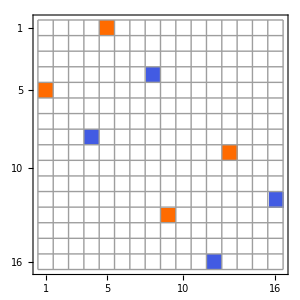

```mathematica
HoldFunction[Normal[#,4]]@QPauliSymbolicProduct[x[2](z[3]+z[4])]//MatrixPlot
```

The eigenvalues of the two generators are quite different.
    The naive one has 2 eigenvalues equal to π and the others are zero.
    The generator with only pairwise interaction has many different eigenvalues. There is almost symmetry with respect to the zero, but the -5.88 eigenvalue violates it.

{-9.03607,-9.0342,-9.03133,-9.0281,-5.88707,-2.75349,-2.74983,-2.74386,0.389371,3.5305,3.53536,3.53595,9.81316,9.81622,9.821,9.82239}

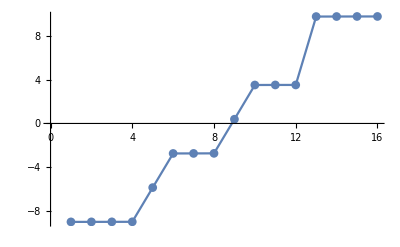

```mathematica
Normal[fredkinPairsDecomposition]//Eigenvalues//Sort
Normal[fredkinPairsDecomposition]//Eigenvalues//Sort//ListPlot[#,Joined->True,PlotMarkers->Automatic]&
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,π,π}

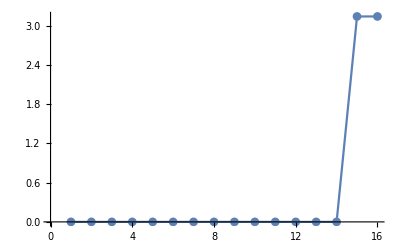

```mathematica
Normal[niceFredkinNaiveGenerator]//Eigenvalues//Sort
Normal[niceFredkinNaiveGenerator]//Eigenvalues//Sort//ListPlot[#,Joined->True,PlotMarkers->Automatic]&
```

Again, as was the case for the Hadamard, the two different generators (naive and pairs-only) commute with each other (with good approximation):

```mathematica
QTimes[#1,#2]-QTimes[#2,#1]&[fredkinPairsDecomposition,niceFredkinNaiveGenerator]//Simplify//Chop
```

(0.-0.00414627 ⅈ) 𝒳[1]-(0.+0.000912617 ⅈ) 𝒳[2]+(0.+0.000608512 ⅈ) 𝒳[3]-(0.+0.000608512 ⅈ) 𝒳[4]+(0.+0.00100117 ⅈ) 𝒴[1]-(0.+0.000694309 ⅈ) 𝒴[2]-(0.+0.000569374 ⅈ) 𝒴[3]+(0.+0.000569374 ⅈ) 𝒴[4]-(0.+0.000113169 ⅈ) 𝒵[3]+(0.+0.000113169 ⅈ) 𝒵[4]+(0.+0.0000173461 ⅈ) 𝒳[3]𝒴[4]-(0.+0.0000173461 ⅈ) 𝒴[3]𝒳[4]+(0.+0.00414627 ⅈ) 𝒳[1]𝒳[3]𝒳[4]-(0.+0.001273 ⅈ) 𝒳[1]𝒳[3]𝒴[4]-(0.+0.000362458 ⅈ) 𝒳[1]𝒳[3]𝒵[4]+(0.+0.001273 ⅈ) 𝒳[1]𝒴[3]𝒳[4]+(0.+0.00414627 ⅈ) 𝒳[1]𝒴[3]𝒴[4]+(0.+0.000498888 ⅈ) 𝒳[1]𝒴[3]𝒵[4]-(0.+0.000255464 ⅈ) 𝒳[1]𝒵[2]𝒳[3]+(0.+0.000255464 ⅈ) 𝒳[1]𝒵[2]𝒳[4]-(0.+0.0018695 ⅈ) 𝒳[1]𝒵[2]𝒴[3]+(0.+0.0018695 ⅈ) 𝒳[1]𝒵[2]𝒴[4]+(0.+0.0058649 ⅈ) 𝒳[1]𝒵[2]𝒵[3]-(0.+0.0058649 ⅈ) 𝒳[1]𝒵[2]𝒵[4]+(0.+0.000362458 ⅈ) 𝒳[1]𝒵[3]𝒳[4]-(0.+0.000498888 ⅈ) 𝒳[1]𝒵[3]𝒴[4]+(0.+0.00414627 ⅈ) 𝒳[1]𝒵[3]𝒵[4]+(0.+0.000912617 ⅈ) 𝒳[2]𝒳[3]𝒳[4]-(0.+0.000743043 ⅈ) 𝒳[2]𝒳[3]𝒴[4]-(0.+0.00103574 ⅈ) 𝒳[2]𝒳[3]𝒵[4]+(0.+0.000743043 ⅈ) 𝒳[2]𝒴[3]𝒳[4]+(0.+0.000912617 ⅈ) 𝒳[2]𝒴[3]𝒴[4]+(0.+0.000795789 ⅈ) 𝒳[2]𝒴[3]𝒵[4]+(0.+0.00103574 ⅈ) 𝒳[2]𝒵[3]𝒳[4]-(0.+0.000795789 ⅈ) 𝒳[2]𝒵[3]𝒴[4]+(0.+0.000912617 ⅈ) 𝒳[2]𝒵[3]𝒵[4]-(0.+0.00100117 ⅈ) 𝒴[1]𝒳[3]𝒳[4]-(0.+0.0058649 ⅈ) 𝒴[1]𝒳[3]𝒴[4]-(0.+0.0018695 ⅈ) 𝒴[1]𝒳[3]𝒵[4]+(0.+0.0058649 ⅈ) 𝒴[1]𝒴[3]𝒳[4]-(0.+0.00100117 ⅈ) 𝒴[1]𝒴[3]𝒴[4]+(0.+0.000255464 ⅈ) 𝒴[1]𝒴[3]𝒵[4]+(0.+0.000498888 ⅈ) 𝒴[1]𝒵[2]𝒳[3]-(0.+0.000498888 ⅈ) 𝒴[1]𝒵[2]𝒳[4]+(0.+0.000362458 ⅈ) 𝒴[1]𝒵[2]𝒴[3]-(0.+0.000362458 ⅈ) 𝒴[1]𝒵[2]𝒴[4]-(0.+0.001273 ⅈ) 𝒴[1]𝒵[2]𝒵[3]+(0.+0.001273 ⅈ) 𝒴[1]𝒵[2]𝒵[4]+(0.+0.0018695 ⅈ) 𝒴[1]𝒵[3]𝒳[4]-(0.+0.000255464 ⅈ) 𝒴[1]𝒵[3]𝒴[4]-(0.+0.00100117 ⅈ) 𝒴[1]𝒵[3]𝒵[4]+(0.+0.000694309 ⅈ) 𝒴[2]𝒳[3]𝒳[4]-(0.+0.00176859 ⅈ) 𝒴[2]𝒳[3]𝒴[4]-(0.+0.000685396 ⅈ) 𝒴[2]𝒳[3]𝒵[4]+(0.+0.00176859 ⅈ) 𝒴[2]𝒴[3]𝒳[4]+(0.+0.000694309 ⅈ) 𝒴[2]𝒴[3]𝒴[4]+(0.+0.000177213 ⅈ) 𝒴[2]𝒴[3]𝒵[4]+(0.+0.000685396 ⅈ) 𝒴[2]𝒵[3]𝒳[4]-(0.+0.000177213 ⅈ) 𝒴[2]𝒵[3]𝒴[4]+(0.+0.000694309 ⅈ) 𝒴[2]𝒵[3]𝒵[4]-(0.+0.000177213 ⅈ) 𝒵[1]𝒳[2]𝒳[3]+(0.+0.000177213 ⅈ) 𝒵[1]𝒳[2]𝒳[4]-(0.+0.000685396 ⅈ) 𝒵[1]𝒳[2]𝒴[3]+(0.+0.000685396 ⅈ) 𝒵[1]𝒳[2]𝒴[4]+(0.+0.00176859 ⅈ) 𝒵[1]𝒳[2]𝒵[3]-(0.+0.00176859 ⅈ) 𝒵[1]𝒳[2]𝒵[4]+(0.+0.0000477399 ⅈ) 𝒵[1]𝒳[3]𝒴[4]-(0.+0.000656409 ⅈ) 𝒵[1]𝒳[3]𝒵[4]+(0.+0.000795789 ⅈ) 𝒵[1]𝒴[2]𝒳[3]-(0.+0.000795789 ⅈ) 𝒵[1]𝒴[2]𝒳[4]+(0.+0.00103574 ⅈ) 𝒵[1]𝒴[2]𝒴[3]-(0.+0.00103574 ⅈ) 𝒵[1]𝒴[2]𝒴[4]-(0.+0.000743043 ⅈ) 𝒵[1]𝒴[2]𝒵[3]+(0.+0.000743043 ⅈ) 𝒵[1]𝒴[2]𝒵[4]-(0.+0.0000477399 ⅈ) 𝒵[1]𝒴[3]𝒳[4]+(0.+0.000263402 ⅈ) 𝒵[1]𝒴[3]𝒵[4]-(0.+0.000608512 ⅈ) 𝒵[1]𝒵[2]𝒳[3]+(0.+0.000608512 ⅈ) 𝒵[1]𝒵[2]𝒳[4]+(0.+0.000569374 ⅈ) 𝒵[1]𝒵[2]𝒴[3]-(0.+0.000569374 ⅈ) 𝒵[1]𝒵[2]𝒴[4]+(0.+0.000113169 ⅈ) 𝒵[1]𝒵[2]𝒵[3]-(0.+0.000113169 ⅈ) 𝒵[1]𝒵[2]𝒵[4]+(0.+0.000656409 ⅈ) 𝒵[1]𝒵[3]𝒳[4]-(0.+0.000263402 ⅈ) 𝒵[1]𝒵[3]𝒴[4]-(0.+0.0000477399 ⅈ) 𝒵[2]𝒳[3]𝒴[4]+(0.+0.000656409 ⅈ) 𝒵[2]𝒳[3]𝒵[4]+(0.+0.0000477399 ⅈ) 𝒵[2]𝒴[3]𝒳[4]-(0.+0.000263402 ⅈ) 𝒵[2]𝒴[3]𝒵[4]-(0.+0.000656409 ⅈ) 𝒵[2]𝒵[3]𝒳[4]+(0.+0.000263402 ⅈ) 𝒵[2]𝒵[3]𝒴[4]-(0.+0.0000173461 ⅈ) 𝒵[1]𝒵[2]𝒳[3]𝒴[4]+(0.+0.0000173461 ⅈ) 𝒵[1]𝒵[2]𝒴[3]𝒳[4]

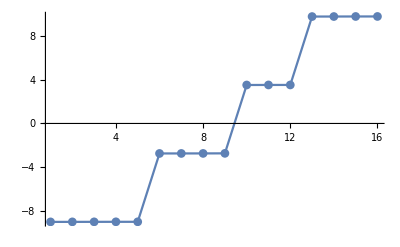
{-9.03609,-9.0342,-9.03133,-9.02864,-9.0281,-2.7535,-2.75235,-2.74983,-2.74373,3.5305,3.53536,3.53595,9.81316,9.81622,9.821,9.82239}
-Graphics-

```mathematica
Column@{#,#//ListPlot[#,Joined->True,PlotRange->All,PlotMarkers->Automatic]&}&@Sort@Eigenvalues[Normal@fredkinPairsDecomposition-Normal@niceFredkinNaiveGenerator]
```

```mathematica
Differences@Sort@Eigenvalues[Normal@fredkinPairsDecomposition-Normal@niceFredkinNaiveGenerator]
```

{0.00188822,0.00287462,0.00269222,0.000541173,6.2746,0.00114968,0.0025186,0.00610047,6.27422,0.00486528,0.000593602,6.2772,0.00305709,0.00478286,0.00139465}

The structure and functioning of the naive generator is quite intuitive (just flip the 2 different “qubits” at (6, 7) and (10, 11)).
The other is a mess, even if there clearly are many symmetries. Mostly is evident the lack of some 3- and 4-qubit interactions terms, like x[2]x[3]x[4], x[1]x[3]x[4], and x[1]x[2](x[3]x[4]+x[3]+x[4]).

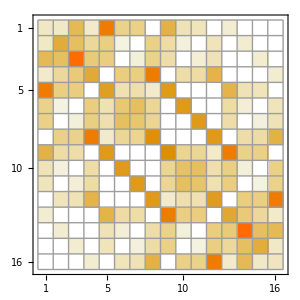
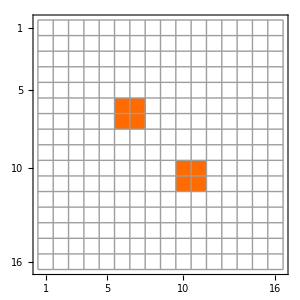

```mathematica
{Normal@fredkinPairsDecomposition//Abs//MatrixPlot,
Normal@niceFredkinNaiveGenerator//Abs//MatrixPlot}
```

## 𝒳𝒳𝒳 gate (that is, MatrixExp[ⅈ 𝒳_1 𝒳_2 𝒳_3]):

This net has been trained with the usual procedure. Starting with all interactions terms and with final average fidelity of 0.9999

```mathematica
𝒳𝒳𝒳PairsDecomposition=interactionsAssToSymbolicProduct@loadInteractionTermsFromJSON[
FileNameJoin@{
"C:\\Users\\lk\\Documents\\docs\\coding\\python\\quantum-gate-learning",
"data","nets","xxx_20170410.json"
},
{2,3,4,1}
];
```

```mathematica
MatrixExp[ⅈ Normal@𝒳𝒳𝒳PairsDecomposition]//Abs//barChart3D
```

-Graphics3D-

```mathematica
Manipulate[
MatrixExp[ⅈ θ Normal@𝒳𝒳𝒳PairsDecomposition]//Abs//barChart3D,
{{θ,0},0,1,0.01,Appearance->"Labeled"}
]
```

## Half-adder

```mathematica
QM`QGates`Private`defineThreeQubitGateFunctions[HalfAdder,
Evaluate[CNot[3,1,2].Toffoli[]]
]
```

```mathematica
takeOnlySomePauliOps[expr_♢QPauliSymbolicProduct,pattern_List,except_:False]:=Cases[expr,
If[TrueQ@except,Except[#,__*pauliOps[__]],#]&[
__*pauliOps[Sequence@@pattern]
],
All
]//Apply@Plus//♢QPauliSymbolicProduct;

removeSmallTerms[♢QPauliSymbolicProduct[expr_],eps_]:=Plus@@Cases[expr,
c_?NumericQ*pauliOps[s__]/;Abs@c>eps
]//♢QPauliSymbolicProduct;
```

### Canonical generator of Fredkin gate

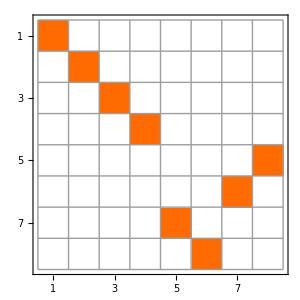
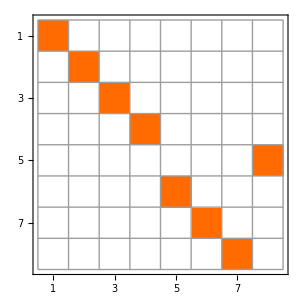

```mathematica
{HalfAdder[]//MatrixPlot,HalfAdder[1,3,2]//MatrixPlot}
```

```mathematica
FullSimplify[decomposeLogWithPaulis@HalfAdder[]]/.s:_[_Integer]:>Style[s,Red,Bold,Larger]
```

1/8 π (-1+𝒳[2] (1+𝒳[3])+𝒴[2]-𝒳[3] (1+𝒴[2])) (-1+𝒵[1])

```mathematica
decomposeLogWithPaulis@HalfAdder[]//QPauliSymbolicProduct
```

(π 1)/8-1/8 π 𝒳[2]+1/8 π 𝒳[3]-1/8 π 𝒴[2]-1/8 π 𝒵[1]-1/8 π 𝒳[2]𝒳[3]+1/8 π 𝒴[2]𝒳[3]+1/8 π 𝒵[1]𝒳[2]-1/8 π 𝒵[1]𝒳[3]+1/8 π 𝒵[1]𝒴[2]+1/8 π 𝒵[1]𝒳[2]𝒳[3]-1/8 π 𝒵[1]𝒴[2]𝒳[3]

```mathematica
QPauliSymbolicProduct[
(1+z[1])/2+(1-z[1])/2((x[2]+ⅈ y[2])/2 x[3]+(x[2]-ⅈ y[2])/2)
]
```

1/2+𝒳[2]/4-1/4 ⅈ 𝒴[2]+𝒵[1]/2+1/4 𝒳[2]𝒳[3]+1/4 ⅈ 𝒴[2]𝒳[3]-1/4 𝒵[1]𝒳[2]+1/4 ⅈ 𝒵[1]𝒴[2]-1/4 𝒵[1]𝒳[2]𝒳[3]-1/4 ⅈ 𝒵[1]𝒴[2]𝒳[3]

```mathematica
QPauliSymbolicProduct[
(1+z[1])/2+(1-z[1])/2((x[2]+ⅈ y[2])/2 x[3]+(x[2]-ⅈ y[2])/2)
]//Normal//MF
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0)

### Results from trained net (fidelity 0.998)

```mathematica
First@FileNames@FileNameJoin@{"C:\\Users\\lk\\Documents\\docs\\coding\\python",
"quantum-gate-learning","data","nets","halfadder*.json"}
```

C:\Users\lk\Documents\docs\coding\python\quantum-gate-learning\data\nets\halfadder_3q+1a_all_f998.json

```mathematica
loadInteractionTermsFromJSON@First@FileNames@FileNameJoin@{"C:\\Users\\lk\\Documents\\docs\\coding\\python",
"quantum-gate-learning","data","nets","halfadder*.json"}
```

<|{1,x}→0.47936,{1,y}→0.124633,{1,z}→4.33278,{2,x}→-0.209019,{2,y}→0.18745,{2,z}→-0.29177,{3,x}→1.43106,{3,y}→-0.902721,{3,z}→0.515117,{4,x}→-5.59582×10^-15,{4,y}→9.27033×10^-16,{4,z}→0.636094,{{1,2},xx}→0.389879,{{1,2},xy}→-0.362595,{{1,2},xz}→-0.161409,{{1,2},yx}→-0.191375,{{1,2},yy}→0.165541,{{1,2},yz}→-0.362811,{{1,2},zx}→-2.99389,{{1,2},zy}→2.95271,{{1,2},zz}→-0.110425,{{1,3},xx}→0.39537,{{1,3},xy}→-0.00687365,{{1,3},xz}→-0.0071211,{{1,3},yx}→-0.194791,{{1,3},yy}→0.00688807,{{1,3},yz}→-0.00776476,{{1,3},zx}→-3.26141,{{1,3},zy}→-1.08678,{{1,3},zz}→0.12896,{{1,4},xx}→4.24071×10^-15,{{1,4},xy}→4.56987×10^-16,{{1,4},xz}→-0.471267,{{1,4},yx}→2.07038×10^-15,{{1,4},yy}→-2.26371×10^-15,{{1,4},yz}→-0.129415,{{1,4},zx}→1.01829×10^-14,{{1,4},zy}→-5.15887×10^-15,{{1,4},zz}→-1.56435,{{2,3},xx}→2.32387,{{2,3},xy}→0.0296328,{{2,3},xz}→-0.0118732,{{2,3},yx}→2.34464,{{2,3},yy}→0.0590961,{{2,3},yz}→-0.0125034,{{2,3},zx}→0.00283691,{{2,3},zy}→-0.0135941,{{2,3},zz}→-0.0431204,{{2,4},xx}→-3.41185×10^-16,{{2,4},xy}→-4.46842×10^-15,{{2,4},xz}→-0.458058,{{2,4},yx}→-9.33226×10^-15,{{2,4},yy}→-5.34198×10^-15,{{2,4},yz}→0.422167,{{2,4},zx}→-5.97072×10^-15,{{2,4},zy}→7.31987×10^-15,{{2,4},zz}→0.174549,{{3,4},xx}→5.77554×10^-15,{{3,4},xy}→-2.85646×10^-15,{{3,4},xz}→-0.805061,{{3,4},yx}→2.79818×10^-15,{{3,4},yy}→3.90547×10^-15,{{3,4},yz}→-0.138653,{{3,4},zx}→4.47051×10^-15,{{3,4},zy}→-2.53246×10^-15,{{3,4},zz}→-0.39613|>

```mathematica
halfadderGenerator=interactionsAssToSymbolicProduct@loadInteractionTermsFromJSON[
First@FileNames@FileNameJoin@{"C:\\Users\\lk\\Documents\\docs\\coding\\python",
"quantum-gate-learning","data","nets","halfadder*.json"},
{2,3,4,1}
]//Chop
```

0.47936 𝒳[2]-0.209019 𝒳[3]+1.43106 𝒳[4]+0.124633 𝒴[2]+0.18745 𝒴[3]-0.902721 𝒴[4]+0.636094 𝒵[1]+4.33278 𝒵[2]-0.29177 𝒵[3]+0.515117 𝒵[4]+0.389879 𝒳[2]𝒳[3]+0.39537 𝒳[2]𝒳[4]-0.362595 𝒳[2]𝒴[3]-0.00687365 𝒳[2]𝒴[4]-0.161409 𝒳[2]𝒵[3]-0.0071211 𝒳[2]𝒵[4]+2.32387 𝒳[3]𝒳[4]+0.0296328 𝒳[3]𝒴[4]-0.0118732 𝒳[3]𝒵[4]-0.191375 𝒴[2]𝒳[3]-0.194791 𝒴[2]𝒳[4]+0.165541 𝒴[2]𝒴[3]+0.00688807 𝒴[2]𝒴[4]-0.362811 𝒴[2]𝒵[3]-0.00776476 𝒴[2]𝒵[4]+2.34464 𝒴[3]𝒳[4]+0.0590961 𝒴[3]𝒴[4]-0.0125034 𝒴[3]𝒵[4]-0.471267 𝒵[1]𝒳[2]-0.458058 𝒵[1]𝒳[3]-0.805061 𝒵[1]𝒳[4]-0.129415 𝒵[1]𝒴[2]+0.422167 𝒵[1]𝒴[3]-0.138653 𝒵[1]𝒴[4]-1.56435 𝒵[1]𝒵[2]+0.174549 𝒵[1]𝒵[3]-0.39613 𝒵[1]𝒵[4]-2.99389 𝒵[2]𝒳[3]-3.26141 𝒵[2]𝒳[4]+2.95271 𝒵[2]𝒴[3]-1.08678 𝒵[2]𝒴[4]-0.110425 𝒵[2]𝒵[3]+0.12896 𝒵[2]𝒵[4]+0.00283691 𝒵[3]𝒳[4]-0.0135941 𝒵[3]𝒴[4]-0.0431204 𝒵[3]𝒵[4]

```mathematica
MatrixExp[-ⅈ Normal@halfadderGenerator]//Abs//barChart3D
```

-Graphics3D-

Interestingly, in this case there are not off-diagonal term for the first qubit. This can be immediately traced back to the lack of 𝒳_1 and 𝒴_1 terms in the corresponding Hamiltonian. Compare this with what we have for the other cases of Fredkin and Toffoli.

Physically, this means no correlation terms for the ancillary qubit during the whole evolution. Weird? Given that the ancillary qubit starts in an eigenstate of 𝒵_1, which is the only interaction term involving it, does this mean the half-adder is actually implementable with only pairwise interactions without the need for the ancilla?

```mathematica
Manipulate[
MatrixExp[ⅈ θ Normal@halfadderGenerator]//Abs//barChart3D[#,RotationAction->"Clip"]&,
{{θ,0},0,1,0.01,Appearance->"Labeled"}
]
```

Let’s look at only the terms involving the ancilla qubit (the first one in this notation). The lack of 𝒳_1 and 𝒴_1 is clear:

```mathematica
halfadderGenerator//Cases[__*pauliOps[___,_[1],___]]//Apply@Plus
```

0.636094 𝒵[1]-0.471267 𝒵[1]𝒳[2]-0.458058 𝒵[1]𝒳[3]-0.805061 𝒵[1]𝒳[4]-0.129415 𝒵[1]𝒴[2]+0.422167 𝒵[1]𝒴[3]-0.138653 𝒵[1]𝒴[4]-1.56435 𝒵[1]𝒵[2]+0.174549 𝒵[1]𝒵[3]-0.39613 𝒵[1]𝒵[4]

Does this mean that the interactions found are actually implementing the half-adder without using the ancilla at all? To verify this, let’s manually remove the 𝒵_1 term from the Hamiltonian, and relabel the other interactions terms to make it a 3 qubit Hamiltonian (with only pairwise interaction terms):

```mathematica
generatorWithoutAncilla=halfadderGenerator/.pauliOps[𝒵[1]]->pauliOps[1]/.pauliOps[𝒵[1],s_]:>pauliOps[s]/.s_[n_Integer]:>s[n-1]
```

0.636094 1+0.0080928 𝒳[1]-0.667077 𝒳[2]+0.626001 𝒳[3]-0.00478177 𝒴[1]+0.609617 𝒴[2]-1.04137 𝒴[3]+2.76843 𝒵[1]-0.11722 𝒵[2]+0.118988 𝒵[3]+0.389879 𝒳[1]𝒳[2]+0.39537 𝒳[1]𝒳[3]-0.362595 𝒳[1]𝒴[2]-0.00687365 𝒳[1]𝒴[3]-0.161409 𝒳[1]𝒵[2]-0.0071211 𝒳[1]𝒵[3]+2.32387 𝒳[2]𝒳[3]+0.0296328 𝒳[2]𝒴[3]-0.0118732 𝒳[2]𝒵[3]-0.191375 𝒴[1]𝒳[2]-0.194791 𝒴[1]𝒳[3]+0.165541 𝒴[1]𝒴[2]+0.00688807 𝒴[1]𝒴[3]-0.362811 𝒴[1]𝒵[2]-0.00776476 𝒴[1]𝒵[3]+2.34464 𝒴[2]𝒳[3]+0.0590961 𝒴[2]𝒴[3]-0.0125034 𝒴[2]𝒵[3]-2.99389 𝒵[1]𝒳[2]-3.26141 𝒵[1]𝒳[3]+2.95271 𝒵[1]𝒴[2]-1.08678 𝒵[1]𝒴[3]-0.110425 𝒵[1]𝒵[2]+0.12896 𝒵[1]𝒵[3]+0.00283691 𝒵[2]𝒳[3]-0.0135941 𝒵[2]𝒴[3]-0.0431204 𝒵[2]𝒵[3]

Exponentiating the above, we indeed get the half-adder. The ancilla was useless after all!

```mathematica
Normal[generatorWithoutAncilla]//MatrixExp[ⅈ #]&//# Exp[-I Arg[#⟦1,1⟧]]&//Chop[#,0.05]&//MF
```

(0.999054 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.999335 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.999469 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.999022 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.998959 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.99899
0 | 0 | 0 | 0 | 0 | 0.999193 | 0 | 0
0 | 0 | 0 | 0 | 0.99919 | 0 | 0 | 0)

```mathematica
Manipulate[
Normal@generatorWithoutAncilla//MatrixExp[-ⅈ θ #]&//Abs//barChart3D,
{{θ,0},0,1,0.01,Appearance->"Labeled"}
]
```

Even considering only terms diagonal in the first qubit (that is, identities and 𝒵_1 factors), we get a pretty decent halfadder:

```mathematica
(* Off diagonal contributions. these are visibly smaller than the diagonal ones: *)
generatorWithoutAncilla/.pauliOps[Except[(𝒴|𝒳)[1]],___]:>0//Chop
(* Contributions to the main diagonal: *)
generatorWithoutAncilla/.pauliOps[(𝒴|𝒳)[1],___]:>0//Chop
```

0.0080928 𝒳[1]-0.00478177 𝒴[1]+0.389879 𝒳[1]𝒳[2]+0.39537 𝒳[1]𝒳[3]-0.362595 𝒳[1]𝒴[2]-0.00687365 𝒳[1]𝒴[3]-0.161409 𝒳[1]𝒵[2]-0.0071211 𝒳[1]𝒵[3]-0.191375 𝒴[1]𝒳[2]-0.194791 𝒴[1]𝒳[3]+0.165541 𝒴[1]𝒴[2]+0.00688807 𝒴[1]𝒴[3]-0.362811 𝒴[1]𝒵[2]-0.00776476 𝒴[1]𝒵[3]

0.636094 1-0.667077 𝒳[2]+0.626001 𝒳[3]+0.609617 𝒴[2]-1.04137 𝒴[3]+2.76843 𝒵[1]-0.11722 𝒵[2]+0.118988 𝒵[3]+2.32387 𝒳[2]𝒳[3]+0.0296328 𝒳[2]𝒴[3]-0.0118732 𝒳[2]𝒵[3]+2.34464 𝒴[2]𝒳[3]+0.0590961 𝒴[2]𝒴[3]-0.0125034 𝒴[2]𝒵[3]-2.99389 𝒵[1]𝒳[2]-3.26141 𝒵[1]𝒳[3]+2.95271 𝒵[1]𝒴[2]-1.08678 𝒵[1]𝒴[3]-0.110425 𝒵[1]𝒵[2]+0.12896 𝒵[1]𝒵[3]+0.00283691 𝒵[2]𝒳[3]-0.0135941 𝒵[2]𝒴[3]-0.0431204 𝒵[2]𝒵[3]

```mathematica
With[{gen=generatorWithoutAncilla/.pauliOps[(𝒴|𝒳)[1],___]:>0//Chop//Echo},
Manipulate[
Normal@gen//MatrixExp[-ⅈ θ #]&//Abs//barChart3D,
{{θ,0},0,1,0.01,Appearance->"Labeled"}
]
]
```

0.636094 1-0.667077 𝒳[2]+0.626001 𝒳[3]+0.609617 𝒴[2]-1.04137 𝒴[3]+2.76843 𝒵[1]-0.11722 𝒵[2]+0.118988 𝒵[3]+2.32387 𝒳[2]𝒳[3]+0.0296328 𝒳[2]𝒴[3]-0.0118732 𝒳[2]𝒵[3]+2.34464 𝒴[2]𝒳[3]+0.0590961 𝒴[2]𝒴[3]-0.0125034 𝒴[2]𝒵[3]-2.99389 𝒵[1]𝒳[2]-3.26141 𝒵[1]𝒳[3]+2.95271 𝒵[1]𝒴[2]-1.08678 𝒵[1]𝒴[3]-0.110425 𝒵[1]𝒵[2]+0.12896 𝒵[1]𝒵[3]+0.00283691 𝒵[2]𝒳[3]-0.0135941 𝒵[2]𝒴[3]-0.0431204 𝒵[2]𝒵[3]

How does this work?

```mathematica
With[{
gen=generatorWithoutAncilla/.pauliOps[(𝒴|𝒳)[1],___]:>0/.{
pauliOps[𝒵[1],s__]:>pauliOps[s],
pauliOps[𝒵[1]]:>pauliOps[1]
}/.s_[n_Integer]:>s[n-1]//Chop[#,0.1]&//Echo
},
Manipulate[
Normal@gen//MatrixExp[-ⅈ θ #]&//Abs//barChart3D,
{{θ,0},0,1,0.01,Appearance->"Labeled"}
]
]
```

3.40453 1-3.66097 𝒳[1]-2.63541 𝒳[2]+3.56233 𝒴[1]-2.12815 𝒴[2]-0.227646 𝒵[1]+0.247947 𝒵[2]+2.32387 𝒳[1]𝒳[2]+2.34464 𝒴[1]𝒳[2]

```mathematica
With[{
gen=generatorWithoutAncilla/.pauliOps[(𝒴|𝒳)[1],___]:>0/.{
pauliOps[𝒵[1],s__]:>-pauliOps[s],
pauliOps[𝒵[1]]:>-pauliOps[1]
}/.s_[n_Integer]:>s[n-1]//Chop[#,0.1]&//Echo
},
Manipulate[
Normal@gen//MatrixExp[-ⅈ θ #]&//Abs//barChart3D,
{{θ,0},0,1,0.01,Appearance->"Labeled"}
]
]
```

-2.13234 1+2.32682 𝒳[1]+3.88742 𝒳[2]-2.34309 𝒴[1]+2.32387 𝒳[1]𝒳[2]+2.34464 𝒴[1]𝒳[2]

## Hadamard

Taking the canonical matrix logarithm of n-qubit Hadamard matrices gives generators containing n-qubit interactions .

```mathematica
hadamard2qb=KP[#,#]&@Hadamard[];
hadamard3qb=KP[#,#,#]&@Hadamard[];
```

```mathematica
FullSimplify@decomposeLogWithPaulis@hadamard2qb/.s_[n_Integer]:>Style[s[n],Bold,Red,Larger]
```

-1/4 π (-2+(𝒳[1]+𝒵[1]) (𝒳[2]+𝒵[2]))

```mathematica
FullSimplify@decomposeLogWithPaulis@hadamard3qb/.s_[n_Integer]:>Style[s[n],Bold,Red,Larger]
```

-1/8 π (-4+√2 (𝒳[1]+𝒵[1]) (𝒳[2]+𝒵[2]) (𝒳[3]+𝒵[3]))

Take the general Hamiltonian generating the Hadamard. For all integer values of ν[n], the following expression when exponentiated correctly gives the Hadamard matrix (as expected).

```mathematica
hadamardGeneralDecomposition=generalHamiltonian@hadamard2qb//pauliBasis//QPauliSymbolicProduct//Expand//Chop
```

1.5708 1-0.785398 𝒳[1]𝒳[2]-0.785398 𝒳[1]𝒵[2]-0.785398 𝒵[1]𝒳[2]-0.785398 𝒵[1]𝒵[2]+1.5708 1 ν[1]+1.0472 𝒳[1] ν[1]+1.0472 𝒳[2] ν[1]+1.0472 𝒵[1] ν[1]+1.0472 𝒵[2] ν[1]+0.523599 𝒳[1]𝒳[2] ν[1]+1.0472 𝒳[1]𝒵[2] ν[1]+0.523599 𝒴[1]𝒴[2] ν[1]+1.0472 𝒵[1]𝒳[2] ν[1]+0.523599 𝒵[1]𝒵[2] ν[1]+1.5708 1 ν[2]-1.0472 𝒳[1] ν[2]-1.0472 𝒳[2] ν[2]-1.0472 𝒵[1] ν[2]-1.0472 𝒵[2] ν[2]+1.0472 𝒳[1]𝒳[2] ν[2]+0.523599 𝒳[1]𝒵[2] ν[2]-0.523599 𝒴[1]𝒴[2] ν[2]+0.523599 𝒵[1]𝒳[2] ν[2]+1.0472 𝒵[1]𝒵[2] ν[2]+1.5708 1 ν[3]-1.5708 𝒳[1]𝒵[2] ν[3]+1.5708 𝒴[1]𝒴[2] ν[3]-1.5708 𝒵[1]𝒳[2] ν[3]+1.5708 1 ν[4]-1.5708 𝒳[1]𝒳[2] ν[4]-1.5708 𝒴[1]𝒴[2] ν[4]-1.5708 𝒵[1]𝒵[2] ν[4]

```mathematica
hadamardGeneralDecomposition/π//DeleteCases[#,__ ν[_],All]&
```

0.5 1-0.25 𝒳[1]𝒳[2]-0.25 𝒳[1]𝒵[2]-0.25 𝒵[1]𝒳[2]-0.25 𝒵[1]𝒵[2]

```mathematica
{Pi/2.,Pi/3.,Pi/6.}
```

{1.5708,1.0472,0.523599}

The ν_1 term is: π/2+π/3(𝒳_1+𝒳_2+𝒵_1+𝒵_2)+π/6(𝒳_1 𝒳_2+𝒴_1 𝒴_2+𝒵_1 𝒵_2)+π/3(𝒳_1 𝒵_2+𝒵_1 𝒳_2)
The ν_2 term is: π/2-π/3(𝒳_1+𝒳_2+𝒵_1+𝒵_2)+π/3(𝒳_1 𝒳_2+1/2 𝒴_1 𝒴_2+𝒵_1 𝒵_2)+π/6(𝒳_1 𝒵_2+𝒵_1 𝒳_2)
The ν_3 term is: π/2+π/2 𝒴_1 𝒴_2-π/2(𝒳_1 𝒵_2+𝒵_1 𝒳_2)
The ν_4 term is: π/2-π/2(𝒳_1 𝒳_2+𝒴_1 𝒴_2+𝒵_1 𝒵_2)

```mathematica
hadamardGeneralDecomposition/π//Rationalize
```

1/2-1/4 𝒳[1]𝒳[2]-1/4 𝒳[1]𝒵[2]-1/4 𝒵[1]𝒳[2]-1/4 𝒵[1]𝒵[2]+1/2 1 ν[1]+1/3 𝒳[1] ν[1]+1/3 𝒳[2] ν[1]+1/3 𝒵[1] ν[1]+1/3 𝒵[2] ν[1]+1/6 𝒳[1]𝒳[2] ν[1]+1/3 𝒳[1]𝒵[2] ν[1]+1/6 𝒴[1]𝒴[2] ν[1]+1/3 𝒵[1]𝒳[2] ν[1]+1/6 𝒵[1]𝒵[2] ν[1]+1/2 1 ν[2]-1/3 𝒳[1] ν[2]-1/3 𝒳[2] ν[2]-1/3 𝒵[1] ν[2]-1/3 𝒵[2] ν[2]+1/3 𝒳[1]𝒳[2] ν[2]+1/6 𝒳[1]𝒵[2] ν[2]-1/6 𝒴[1]𝒴[2] ν[2]+1/6 𝒵[1]𝒳[2] ν[2]+1/3 𝒵[1]𝒵[2] ν[2]+1/2 1 ν[3]-1/2 𝒳[1]𝒵[2] ν[3]+1/2 𝒴[1]𝒴[2] ν[3]-1/2 𝒵[1]𝒳[2] ν[3]+1/2 1 ν[4]-1/2 𝒳[1]𝒳[2] ν[4]-1/2 𝒴[1]𝒴[2] ν[4]-1/2 𝒵[1]𝒵[2] ν[4]

```mathematica
Table[
DeleteCases[hadamardGeneralDecomposition/π,Except[___*ν[n],_Times],All]//Simplify,
{n,Range@4}
]//Rationalize//Column
```

(1/2+𝒳[1]/3+𝒳[2]/3+𝒵[1]/3+𝒵[2]/3+1/6 𝒳[1]𝒳[2]+1/3 𝒳[1]𝒵[2]+1/6 𝒴[1]𝒴[2]+1/3 𝒵[1]𝒳[2]+1/6 𝒵[1]𝒵[2]) ν[1]
(1/2-𝒳[1]/3-𝒳[2]/3-𝒵[1]/3-𝒵[2]/3+1/3 𝒳[1]𝒳[2]+1/6 𝒳[1]𝒵[2]-1/6 𝒴[1]𝒴[2]+1/6 𝒵[1]𝒳[2]+1/3 𝒵[1]𝒵[2]) ν[2]
(1/2-1/2 𝒳[1]𝒵[2]+1/2 𝒴[1]𝒴[2]-1/2 𝒵[1]𝒳[2]) ν[3]
(1/2-1/2 𝒳[1]𝒳[2]-1/2 𝒴[1]𝒴[2]-1/2 𝒵[1]𝒵[2]) ν[4]

These terms can be equivalently found by decomposing the projectors over the eigenvectors in terms of Pauli matrices:

```mathematica
hadamard2qb//N//Eigenvectors//Map[
QPauliSymbolicProduct@Rationalize@Chop@pauliBasis@KP[#,#]&
]//Column
```

1/4+𝒳[1]/6+𝒳[2]/6+𝒵[1]/6+𝒵[2]/6+1/12 𝒳[1]𝒳[2]+1/6 𝒳[1]𝒵[2]+1/12 𝒴[1]𝒴[2]+1/6 𝒵[1]𝒳[2]+1/12 𝒵[1]𝒵[2]
1/4-𝒳[1]/6-𝒳[2]/6-𝒵[1]/6-𝒵[2]/6+1/6 𝒳[1]𝒳[2]+1/12 𝒳[1]𝒵[2]-1/12 𝒴[1]𝒴[2]+1/12 𝒵[1]𝒳[2]+1/6 𝒵[1]𝒵[2]
1/4-1/4 𝒳[1]𝒵[2]+1/4 𝒴[1]𝒴[2]-1/4 𝒵[1]𝒳[2]
1/4-1/4 𝒳[1]𝒳[2]-1/4 𝒴[1]𝒴[2]-1/4 𝒵[1]𝒵[2]

```mathematica
Eigenvectors@N@hadamard2qb//MF
```

(0.816497 | 0.408248 | 0.408248 | 0
0.288675 | -0.288675 | -0.288675 | 0.866025
0.5 | -0.5 | -0.5 | -0.5
0 | 0.707107 | -0.707107 | 0)

The terms attached with the ν coefficients all exponentiate to the identity matrix:

```mathematica
Table[
ReplaceAll[
hadamardGeneralDecomposition//DeleteCases[#,Except[___*ν[n],_Times],All]&,
ν[n]->RandomInteger[{1,10}]
]//Normal//MatrixExp[ⅈ #]&//Chop,
{n,1,4}
]//Map@MF
```

{(1. | 0 | 0 | 0
0 | 1. | 0 | 0
0 | 0 | 1. | 0
0 | 0 | 0 | 1.),(1. | 0 | 0 | 0
0 | 1. | 0 | 0
0 | 0 | 1. | 0
0 | 0 | 0 | 1.),(1. | 0 | 0 | 0
0 | 1. | 0 | 0
0 | 0 | 1. | 0
0 | 0 | 0 | 1.),(1. | 0 | 0 | 0
0 | 1. | 0 | 0
0 | 0 | 1. | 0
0 | 0 | 0 | 1.)}

And they all commute with the fixed term:

```mathematica
Table[
With[{fixedTerm=hadamardGeneralDecomposition/.ν[_]->0//Chop},
Block[{firstTerm,secondTerm},
firstTerm=QTimes[
hadamardGeneralDecomposition//DeleteCases[#,Except[___*ν[n],_Times],All]&,
fixedTerm
]//Chop;
secondTerm=QTimes[
fixedTerm,
hadamardGeneralDecomposition//DeleteCases[#,Except[___*ν[n],_Times],All]&
]//Chop;

Panel@Column@{firstTerm,secondTerm}
]
],
{n,4}
]
```

{0
0,0
0,4.9348 1 ν[3]-4.9348 𝒳[1]𝒵[2] ν[3]+4.9348 𝒴[1]𝒴[2] ν[3]-4.9348 𝒵[1]𝒳[2] ν[3]
4.9348 1 ν[3]-4.9348 𝒳[1]𝒵[2] ν[3]+4.9348 𝒴[1]𝒴[2] ν[3]-4.9348 𝒵[1]𝒳[2] ν[3],4.9348 1 ν[4]-4.9348 𝒳[1]𝒳[2] ν[4]-4.9348 𝒴[1]𝒴[2] ν[4]-4.9348 𝒵[1]𝒵[2] ν[4]
4.9348 1 ν[4]-4.9348 𝒳[1]𝒳[2] ν[4]-4.9348 𝒴[1]𝒴[2] ν[4]-4.9348 𝒵[1]𝒵[2] ν[4]}

And their product is always zero

```mathematica
Table[
Block[{firstTerm,secondTerm},
firstTerm=hadamardGeneralDecomposition//DeleteCases[#,Except[___*ν[nm⟦1⟧],_Times],All]&;
secondTerm=hadamardGeneralDecomposition//DeleteCases[#,Except[___*ν[nm⟦2⟧],_Times],All]&;

Panel@Column@{
nm,
firstTerm,secondTerm,
QTimes[firstTerm,secondTerm]
(*,♢QPauliSymbolicProduct@CenterDot[First@secondTerm,First@firstTerm]*)
}
],
{nm,Subsets[Range@4,{2}]}
]//Chop
```

{{1,2}
1.5708 1 ν[1]+1.0472 𝒳[1] ν[1]+1.0472 𝒳[2] ν[1]+1.0472 𝒵[1] ν[1]+1.0472 𝒵[2] ν[1]+0.523599 𝒳[1]𝒳[2] ν[1]+1.0472 𝒳[1]𝒵[2] ν[1]+0.523599 𝒴[1]𝒴[2] ν[1]+1.0472 𝒵[1]𝒳[2] ν[1]+0.523599 𝒵[1]𝒵[2] ν[1]
1.5708 1 ν[2]-1.0472 𝒳[1] ν[2]-1.0472 𝒳[2] ν[2]-1.0472 𝒵[1] ν[2]-1.0472 𝒵[2] ν[2]+1.0472 𝒳[1]𝒳[2] ν[2]+0.523599 𝒳[1]𝒵[2] ν[2]-0.523599 𝒴[1]𝒴[2] ν[2]+0.523599 𝒵[1]𝒳[2] ν[2]+1.0472 𝒵[1]𝒵[2] ν[2]
0,{1,3}
1.5708 1 ν[1]+1.0472 𝒳[1] ν[1]+1.0472 𝒳[2] ν[1]+1.0472 𝒵[1] ν[1]+1.0472 𝒵[2] ν[1]+0.523599 𝒳[1]𝒳[2] ν[1]+1.0472 𝒳[1]𝒵[2] ν[1]+0.523599 𝒴[1]𝒴[2] ν[1]+1.0472 𝒵[1]𝒳[2] ν[1]+0.523599 𝒵[1]𝒵[2] ν[1]
1.5708 1 ν[3]-1.5708 𝒳[1]𝒵[2] ν[3]+1.5708 𝒴[1]𝒴[2] ν[3]-1.5708 𝒵[1]𝒳[2] ν[3]
0,{1,4}
1.5708 1 ν[1]+1.0472 𝒳[1] ν[1]+1.0472 𝒳[2] ν[1]+1.0472 𝒵[1] ν[1]+1.0472 𝒵[2] ν[1]+0.523599 𝒳[1]𝒳[2] ν[1]+1.0472 𝒳[1]𝒵[2] ν[1]+0.523599 𝒴[1]𝒴[2] ν[1]+1.0472 𝒵[1]𝒳[2] ν[1]+0.523599 𝒵[1]𝒵[2] ν[1]
1.5708 1 ν[4]-1.5708 𝒳[1]𝒳[2] ν[4]-1.5708 𝒴[1]𝒴[2] ν[4]-1.5708 𝒵[1]𝒵[2] ν[4]
0,{2,3}
1.5708 1 ν[2]-1.0472 𝒳[1] ν[2]-1.0472 𝒳[2] ν[2]-1.0472 𝒵[1] ν[2]-1.0472 𝒵[2] ν[2]+1.0472 𝒳[1]𝒳[2] ν[2]+0.523599 𝒳[1]𝒵[2] ν[2]-0.523599 𝒴[1]𝒴[2] ν[2]+0.523599 𝒵[1]𝒳[2] ν[2]+1.0472 𝒵[1]𝒵[2] ν[2]
1.5708 1 ν[3]-1.5708 𝒳[1]𝒵[2] ν[3]+1.5708 𝒴[1]𝒴[2] ν[3]-1.5708 𝒵[1]𝒳[2] ν[3]
0,{2,4}
1.5708 1 ν[2]-1.0472 𝒳[1] ν[2]-1.0472 𝒳[2] ν[2]-1.0472 𝒵[1] ν[2]-1.0472 𝒵[2] ν[2]+1.0472 𝒳[1]𝒳[2] ν[2]+0.523599 𝒳[1]𝒵[2] ν[2]-0.523599 𝒴[1]𝒴[2] ν[2]+0.523599 𝒵[1]𝒳[2] ν[2]+1.0472 𝒵[1]𝒵[2] ν[2]
1.5708 1 ν[4]-1.5708 𝒳[1]𝒳[2] ν[4]-1.5708 𝒴[1]𝒴[2] ν[4]-1.5708 𝒵[1]𝒵[2] ν[4]
0,{3,4}
1.5708 1 ν[3]-1.5708 𝒳[1]𝒵[2] ν[3]+1.5708 𝒴[1]𝒴[2] ν[3]-1.5708 𝒵[1]𝒳[2] ν[3]
1.5708 1 ν[4]-1.5708 𝒳[1]𝒳[2] ν[4]-1.5708 𝒴[1]𝒴[2] ν[4]-1.5708 𝒵[1]𝒵[2] ν[4]
0}

In fact, all terms are 2π times the projector on some eigenvector. As also shown by their being equal to their squares.

```mathematica
Table[
Block[{firstTerm,secondTerm},
firstTerm=hadamardGeneralDecomposition//DeleteCases[#,Except[___*ν[n],_Times],All]&;
firstTerm=firstTerm/(2π)/ν[n]//Chop;

Panel@Column@{
firstTerm,
Chop@QTimes[firstTerm,firstTerm]
}
],
{n,Range@4}
]
```

{0.25 1+0.166667 𝒳[1]+0.166667 𝒳[2]+0.166667 𝒵[1]+0.166667 𝒵[2]+0.0833333 𝒳[1]𝒳[2]+0.166667 𝒳[1]𝒵[2]+0.0833333 𝒴[1]𝒴[2]+0.166667 𝒵[1]𝒳[2]+0.0833333 𝒵[1]𝒵[2]
0.25 1+0.166667 𝒳[1]+0.166667 𝒳[2]+0.166667 𝒵[1]+0.166667 𝒵[2]+0.0833333 𝒳[1]𝒳[2]+0.166667 𝒳[1]𝒵[2]+0.0833333 𝒴[1]𝒴[2]+0.166667 𝒵[1]𝒳[2]+0.0833333 𝒵[1]𝒵[2],0.25 1-0.166667 𝒳[1]-0.166667 𝒳[2]-0.166667 𝒵[1]-0.166667 𝒵[2]+0.166667 𝒳[1]𝒳[2]+0.0833333 𝒳[1]𝒵[2]-0.0833333 𝒴[1]𝒴[2]+0.0833333 𝒵[1]𝒳[2]+0.166667 𝒵[1]𝒵[2]
0.25 1-0.166667 𝒳[1]-0.166667 𝒳[2]-0.166667 𝒵[1]-0.166667 𝒵[2]+0.166667 𝒳[1]𝒳[2]+0.0833333 𝒳[1]𝒵[2]-0.0833333 𝒴[1]𝒴[2]+0.0833333 𝒵[1]𝒳[2]+0.166667 𝒵[1]𝒵[2],0.25 1-0.25 𝒳[1]𝒵[2]+0.25 𝒴[1]𝒴[2]-0.25 𝒵[1]𝒳[2]
0.25 1-0.25 𝒳[1]𝒵[2]+0.25 𝒴[1]𝒴[2]-0.25 𝒵[1]𝒳[2],0.25 1-0.25 𝒳[1]𝒳[2]-0.25 𝒴[1]𝒴[2]-0.25 𝒵[1]𝒵[2]
0.25 1-0.25 𝒳[1]𝒳[2]-0.25 𝒴[1]𝒴[2]-0.25 𝒵[1]𝒵[2]}